```mathematica
Clear["Global`*"]
```

```mathematica
eq10=g==(1-z)*gy+z* gz
eq11=g2==(1-z)*gy^2+z*gz^2
eq8b=gy=Qdg*g+1-g
eq8c=gz=g2*(Qcg-Qdg)+Qdg*g+1-g
```

```mathematica
eq10into8=Simplify[(1-z)*gy+z* gz-g/.{gy->Qdg*g+1-g,gz-> g2*(Qcg-Qdg)+Qdg*g+1-g}]
```

1+g (-2+Qdg)+g2 (Qcg-Qdg) z

```mathematica
Collect[eq10into8,z]
```

1+g (-2+Qdg)+g2 (Qcg-Qdg) z

```mathematica
eq13=g2 (Qcg-Qdg) z==g (2-Qdg)-1
```

```mathematica
(1-z)*gy+z* gz-g/.{gy->Qdg*g+1-g}
```

-g+(1-g+g Qdg) (1-z)+gz z

```mathematica
eq14=gz z== g-(1-g+g Qdg) (1-z)
```

```mathematica
Simplify[Expand[(1-z)*gy^2+gz1*gz2-g2/.{gy->Qdg*g+1-g,gz1->g2*(Qcg-Qdg)+Qdg*g+1-g,gz2-> g-(1-g+g Qdg) (1-z)}]]
```

g+g^2 (-1+Qdg)+g g2 (Qcg-Qdg) (2+Qdg (-1+z)-z)+g2 (-1+Qdg+Qcg (-1+z)-Qdg z)

```mathematica
Collect[1-2 g+g^2-g2+2 g Qdg-2 g^2 Qdg+g^2 Qdg^2+2 g2 Qcg z-2 g g2 Qcg z+g2^2 Qcg^2 z-2 g2 Qdg z+2 g g2 Qdg z+2 g g2 Qcg Qdg z-2 g2^2 Qcg Qdg z-2 g g2 Qdg^2 z+g2^2 Qdg^2 z,z]
```

1-2 g+g^2-g2+2 g Qdg-2 g^2 Qdg+g^2 Qdg^2+(2 g2 Qcg-2 g g2 Qcg+g2^2 Qcg^2-2 g2 Qdg+2 g g2 Qdg+2 g g2 Qcg Qdg-2 g2^2 Qcg Qdg-2 g g2 Qdg^2+g2^2 Qdg^2) z

```mathematica
Collect[2 g2 Qcg-2 g g2 Qcg+g2^2 Qcg^2-2 g2 Qdg+2 g g2 Qdg+2 g g2 Qcg Qdg-2 g2^2 Qcg Qdg-2 g g2 Qdg^2+g2^2 Qdg^2,g]
```

2 g2 Qcg+g2^2 Qcg^2-2 g2 Qdg-2 g2^2 Qcg Qdg+g2^2 Qdg^2+g (-2 g2 Qcg+2 g2 Qdg+2 g2 Qcg Qdg-2 g2 Qdg^2)

```mathematica
Simplify[(-2 g2 Qcg+2 g2 Qdg+2 g2 Qcg Qdg-2 g2 Qdg^2)*g-(1-g+g Qdg) (1-z)+z*(2 g2 Qcg+g2^2 Qcg^2-2 g2 Qdg-2 g2^2 Qcg Qdg+g2^2 Qdg^2)+1-2 g+g^2-g2+2 g Qdg-2 g^2 Qdg+g^2 Qdg^2]
```

g^2 (-1+Qdg)^2+z+g2^2 (Qcg-Qdg)^2 z+g (-1+Qdg) (1+2 g2 (Qcg-Qdg)+z)+g2 (-1+2 Qcg z-2 Qdg z)

```mathematica
Collect[g^2 (-1+Qdg)^2+z+g2^2 (Qcg-Qdg)^2 z+g (-1+Qdg) (1+2 g2 (Qcg-Qdg)+z)+g2 (-1+2 Qcg z-2 Qdg z)==0,g2]
```

g (-1+Qdg)+g^2 (-1+Qdg)^2+z+g2^2 (Qcg-Qdg)^2 z+g (-1+Qdg) z+g2 (-1+2 g (Qcg-Qdg) (-1+Qdg)+2 Qcg z-2 Qdg z)==0

```mathematica
Qcg=ϵ*Pcg+(1-ϵ)*Pdg
Qdg=(1-e)*Pdg+e*Pcg
Pcg=ϵ*g/(ϵ*g+e*(1-g))
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g))
Plot[f=r(2*g-1-Qdg*g)-g//.{r-> 4,ϵ->(1-e)^2+e^2,e-> 0.074},{g,0,1}]
```

(g (1-ϵ)^2)/((1-e) (1-g)+g (1-ϵ))+(g ϵ^2)/(e (1-g)+g ϵ)

((1-e) g (1-ϵ))/((1-e) (1-g)+g (1-ϵ))+(e g ϵ)/(e (1-g)+g ϵ)

(g ϵ)/(e (1-g)+g ϵ)

(g (1-ϵ))/((1-e) (1-g)+g (1-ϵ))

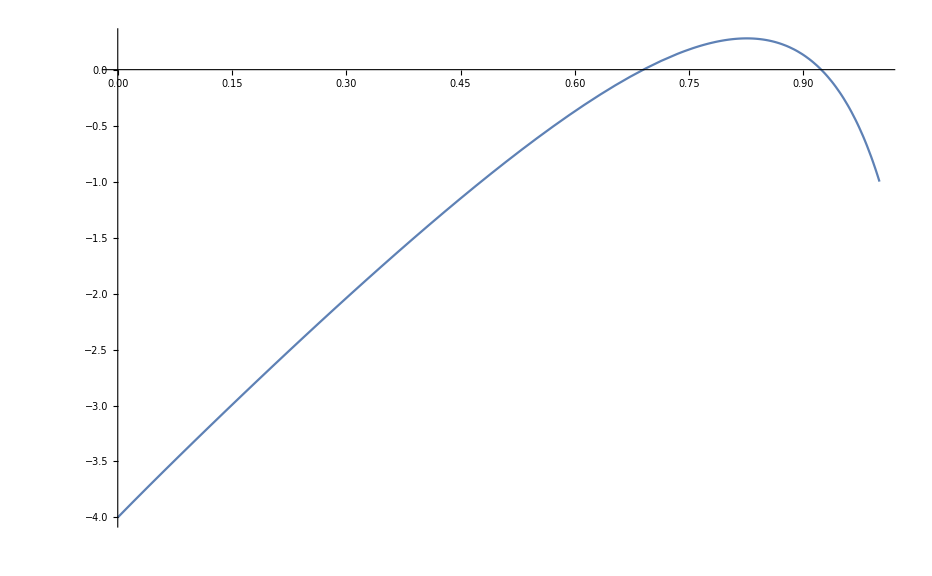

```mathematica
Plot[f=r(2*g-1-Qdg*g)-g//.{r-> 4,ϵ->(1-e)^2+e^2,e-> 0.074},{g,0,1}]
```

```mathematica
f=r(2*g-1-Qdg*g)-g
```

```mathematica
Simplify[-g+r (-1+2 g-g (((1-e) g (1-ϵ))/((1-e) (1-g)+g (1-ϵ))+(e g ϵ)/(e (1-g)+g ϵ)))]
```

-g+r (-1+2 g+(g^2 (e+e^2 (-1+g)-e g-g (-1+ϵ) ϵ))/((e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ)))

```mathematica
polyf =(-g+r (-1+2 g))*(e (-1+g)-g ϵ)*(1+e (-1+g)-g ϵ)+r*g^2 (e+e^2 (-1+g)-e g-g (-1+ϵ) ϵ)
```

(-g+(-1+2 g) r) (e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ)+g^2 r (e+e^2 (-1+g)-e g-g (-1+ϵ) ϵ)

```mathematica
Collect[polyf,g]
```

e r-e^2 r+g (e-e^2-3 e r+4 e^2 r+r ϵ-2 e r ϵ)+g^2 (-e+2 e^2+3 e r-6 e^2 r+ϵ-2 e ϵ-2 r ϵ+6 e r ϵ-r ϵ^2)+g^3 (-e^2-e r+3 e^2 r+2 e ϵ-4 e r ϵ-r (-1+ϵ) ϵ-ϵ^2+2 r ϵ^2)

```mathematica
f/.{r-> 3,e-> 0.01,ϵ->0.99^2+0.01^2,g->0.59}
```

-0.116597

```mathematica
Solve[{D[f,g]==0,f==0},r]
```

{}

```mathematica
Simplify[D[f,g]-r(2*g-1-Qdg*g)+g]
```

-1+g+3 r-2 g r+((-1+e) g^2 r (e-ϵ) (-1+ϵ))/(1+e (-1+g)-g ϵ)^2-(2 (-1+e) g r (-1+ϵ))/(1+e (-1+g)-g ϵ)+((-1+e) g^2 r (-1+ϵ))/(1+e (-1+g)-g ϵ)+(e g^2 r ϵ (-e+ϵ))/(e-e g+g ϵ)^2-(2 e g r ϵ)/(e-e g+g ϵ)+(e g^2 r ϵ)/(e-e g+g ϵ)

```mathematica
Solve[r(2*g-1-Qdg*g)-g==0,r]
```

{{r→g/(-1+2 g-g (((1-e) g (1-ϵ))/((1-e) (1-g)+g (1-ϵ))+(e g ϵ)/(e (1-g)+g ϵ)))}}

```mathematica
Qdgz=(((1-e) g[z] (1-ϵ))/((1-e) (1-g[z])+g[z] (1-ϵ))+(e g[z] ϵ)/(e (1-g[z])+g[z] ϵ)) 
fprime=D[r(2*g[z]-1-Qdgz*g[z])-g[z],z]
```

((1-e) (1-ϵ) g[z])/((1-e) (1-g[z])+(1-ϵ) g[z])+(e ϵ g[z])/(e (1-g[z])+ϵ g[z])

-g'[z]+r (2 g'[z]-(((1-e) (1-ϵ) g[z])/((1-e) (1-g[z])+(1-ϵ) g[z])+(e ϵ g[z])/(e (1-g[z])+ϵ g[z])) g'[z]-g[z] (((1-e) (1-ϵ) g'[z])/((1-e) (1-g[z])+(1-ϵ) g[z])+(e ϵ g'[z])/(e (1-g[z])+ϵ g[z])-((1-e) (1-ϵ) g[z] (-(1-e) g'[z]+(1-ϵ) g'[z]))/((1-e) (1-g[z])+(1-ϵ) g[z])^2-(e ϵ g[z] (-e g'[z]+ϵ g'[z]))/(e (1-g[z])+ϵ g[z])^2))

```mathematica
Qdgz=(((1-e) g (1-ϵ))/((1-e) (1-g)+g (1-ϵ))+(e g ϵ)/(e (1-g)+g ϵ))
```

((1-e) g (1-ϵ))/((1-e) (1-g)+g (1-ϵ))+(e g ϵ)/(e (1-g)+g ϵ)

```mathematica
Factor[Qdgz]
```

-(g (e-e^2-e g+e^2 g+g ϵ-g ϵ^2))/((-e+e g-g ϵ) (1-e+e g-g ϵ))

```mathematica
polyf =(-g+r (-1+2 g))*(e (-1+g)-g ϵ)*(1+e (-1+g)-g ϵ)+r*g^2 (e+e^2 (-1+g)-e g-g (-1+ϵ) ϵ)
```

(-g+(-1+2 g) r) (e (-1+g)-g ϵ) (1+e (-1+g)-g ϵ)+g^2 r (e+e^2 (-1+g)-e g-g (-1+ϵ) ϵ)

```mathematica
polyf=(-g+r (-1+2 g))*(e (1-g)+g ϵ)*((1-e) (1-g)+g(1- ϵ))+r*g^2 (e-e^2-e g+e^2 g+g ϵ-g ϵ^2)
```

(-g+(-1+2 g) r) ((1-e) (1-g)+g (1-ϵ)) (e (1-g)+g ϵ)+g^2 r (e-e^2-e g+e^2 g+g ϵ-g ϵ^2)

```mathematica
Simplify[polyf2-polyf]
```

-2 (-r+g (-1+2 r)) (e^2 (-1+g)^2+g ϵ (-1+g ϵ)-e (-1+g) (-1+2 g ϵ))

```mathematica
Collect[polyf,g]
```

e r-e^2 r+g (e-e^2-3 e r+4 e^2 r+r ϵ-2 e r ϵ)+g^2 (-e+2 e^2+3 e r-6 e^2 r+ϵ-2 e ϵ-2 r ϵ+6 e r ϵ-r ϵ^2)+g^3 (-e^2-e r+3 e^2 r+2 e ϵ-4 e r ϵ-r (-1+ϵ) ϵ-ϵ^2+2 r ϵ^2)

```mathematica
polyfnum=Collect[polyf,g]//.{r-> 4,e-> 0.01,ϵ->(1-e)^2+e^2}
```

-0.0396-3.73388 g+10.4603 g^2-6.55098 g^3

```mathematica
Roots[polyfnum==0,g]
```

g==-0.0103061||g==0.560371||g==1.04669

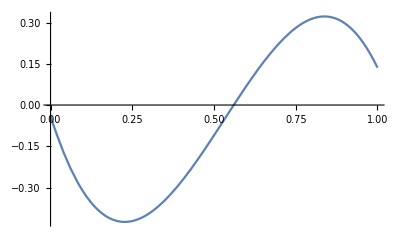

```mathematica
Plot[polyfnum==0,{g,0,1}]
```

```mathematica
a=-e^2-e r+3 e^2 r+2 e ϵ-4 e r ϵ-r (-1+ϵ) ϵ-ϵ^2+2 r ϵ^2;
b=-e+2 e^2+3 e r-6 e^2 r+ϵ-2 e ϵ-2 r ϵ+6 e r ϵ-r ϵ^2;
c=e-e^2-3 e r+4 e^2 r+r ϵ-2 e r ϵ;
d=e r-e^2 r;
```

```mathematica
Δ=18*a*b*c*d-4*d*b^3+(b*c)^2-4*a*c^3-27*(a*d)^2;
```

```mathematica
NSolve[Δ==0/.{r->3, ϵ->(1-e)^2+e^2},e]
```

{{e→-0.581143},{e→0.0744656},{e→0.377305-0.152848 ⅈ},{e→0.377305+0.152848 ⅈ},{e→0.526154+0.238728 ⅈ},{e→0.526154-0.238728 ⅈ},{e→0.537408+0.539755 ⅈ},{e→0.537408-0.539755 ⅈ},{e→0.999546},{e→0.999608},{e→1.00052},{e→1.00062},{e→2.49994}}

```mathematica
Simplify[-e^2-e r+3 e^2 r+2 e ϵ-4 e r ϵ-r (-1+ϵ) ϵ-ϵ^2+2 r ϵ^2]
```

(e-ϵ) (e (-1+3 r)+ϵ-r (1+ϵ))

```mathematica
Simplify[-e+2 e^2+3 e r-6 e^2 r+ϵ-2 e ϵ-2 r ϵ+6 e r ϵ-r ϵ^2]
```

e^2 (2-6 r)+ϵ-r ϵ (2+ϵ)+e (-1+3 r) (1+2 ϵ)

```mathematica
Simplify[e-e^2-3 e r+4 e^2 r+r ϵ-2 e r ϵ]
```

e+e^2 (-1+4 r)+r ϵ-e r (3+2 ϵ)

```mathematica
Simplify[e r-e^2 r]
```

-(-1+e) e r

```mathematica
Plot[Qdg==0//.{r->3, ϵ->(1-e)^2+e^2,e-> 0.01},g]
```

Plot[Qdg==0//.{r→3,ϵ→(1-e)^2+e^2,e→0.01},g]

```mathematica
Qdg
```

((1-e) g (1-ϵ))/((1-e) (1-g)+g (1-ϵ))+(e g ϵ)/(e (1-g)+g ϵ)

```mathematica
(e (-1+3 r)+ϵ-r (1+ϵ))/.{r->1.1}
```

```mathematica
Simplify[2.3 e+ϵ-1.1 (1+ϵ)]//.{e-> 0.5,ϵ-> (1-e)^2-e^2}
```

0.05

```mathematica
Simplify[0.5 (-1+3 r)+ϵ-r (1+ϵ)]
```

-0.5+r (0.5-1. ϵ)+ϵ

```mathematica
e (-1+3 r)+ϵ-r (1+ϵ)//.{ϵ-> (1-e)^2-e^2}
```

(1-e)^2-e^2-(1+(1-e)^2-e^2) r+e (-1+3 r)

```mathematica
Solve[(1-e)^2-e^2-(1+(1-e)^2-e^2) r+e (-1+3 r)==0,r]
```

{{r→(-1+3 e)/(-2+5 e)}}

```mathematica
Reduce[e+e^2 (-1+4 r)+r ϵ-e r (3+2 ϵ)>0&&1>ϵ>0.5>e>0&&r>1]
```

(0<e≤0.146447&&0.5<ϵ<1.&&r>1.)||(0.146447<e≤0.211325&&((0.5<ϵ<(-3. e+4. e^2)/(-1.+2. e)&&1.<r<(-1. e+e^2)/(-3. e+4. e^2+ϵ-2. e ϵ))||((-3. e+4. e^2)/(-1.+2. e)≤ϵ<1.&&r>1.)))||(0.211325<e≤0.25&&(((-2. e+3. e^2)/(-1.+2. e)<ϵ<(-3. e+4. e^2)/(-1.+2. e)&&1.<r<(-1. e+e^2)/(-3. e+4. e^2+ϵ-2. e ϵ))||((-3. e+4. e^2)/(-1.+2. e)≤ϵ<1.&&r>1.)))||(0.25<e<0.333333&&(-2. e+3. e^2)/(-1.+2. e)<ϵ<1.&&1.<r<(-1. e+e^2)/(-3. e+4. e^2+ϵ-2. e ϵ))

```mathematica
Collect[b,r]
```

-e+2 e^2+ϵ-2 e ϵ+r (3 e-6 e^2-2 ϵ+6 e ϵ-ϵ^2)

```mathematica
Simplify[3 e-6 e^2-2 ϵ+6 e ϵ-ϵ]
```

-3 (-1+2 e) (e-ϵ)

```mathematica
Simplify[-e+2 e^2+ϵ-2 e ϵ]
```

(-1+2 e) (e-ϵ)

```mathematica
Simplify[(ϵ-e)*(1-2*e)*(1-3 r)-b]
```

r (-1+ϵ) ϵ

```mathematica
Collect[c,r]
```

e-e^2+r (-3 e+4 e^2+ϵ-2 e ϵ)

```mathematica
Simplify[-3 e+4 e^2+ϵ-2 e ϵ]
```

4 e^2+ϵ-e (3+2 ϵ)

```mathematica
Reduce[b<0&&1>ϵ>0.5&&0.5>e>0&&r>1]
```

0.5<ϵ<1.&&((0<e≤0.5 ϵ&&r>1.)||(0.5 ϵ<e<0.25 (1.+2. ϵ)-0.144338 √(3.-4. ϵ+4. ϵ^2)&&r>(-1. e+2. e^2+ϵ-2. e ϵ)/(-3. e+6. e^2+2. ϵ-6. e ϵ+ϵ^2)))

```mathematica
Assuming[1>ϵ>0.5&&0.5>e>0&&r>1,FullSimplify@Reduce[c>0]]
```

4 e^2+ϵ==e (3+2 ϵ)||e (e+r (3+2 ϵ))<e+4 e^2 r+r ϵ

```mathematica
Assuming[1>ϵ>0.5&&0.5>e>0&&r>1,FullSimplify@Reduce[b>0]]
```

12 e+√(9+12 (-1+ϵ) ϵ)==3+6 ϵ||12 e+√(9+12 (-1+ϵ) ϵ)>3+6 ϵ||r<((-1+2 e) (e-ϵ))/(6 e^2+ϵ (2+ϵ)-3 e (1+2 ϵ))

```mathematica
Assuming[4 e^2+ϵ==e (3+2 ϵ)&&1>ϵ>0.5&&0.5>e>0&&r>1,FullSimplify@Reduce[b<0]]
```

True

```mathematica
Reduce[12 e+√(9+12 (-1+ϵ) ϵ)-3+6 ϵ>0/.{ϵ->(-3 e+4 e^2)/(-1+2 e)}]
```

0<e<1/2||e>Root0.582Root[-6+55 #1-128 #1^2+88 #1^3&,2]0.5823105498785195

```mathematica
Simplify[1/12 (3+6 ϵ-√3 √(3-4 ϵ+4 ϵ^2))/.{ϵ->(-3 e+4 e^2)/(-1+2 e)}]
```

1/4+(3 e)/(2-4 e)+(2 e^2)/(-1+2 e)-(√((3-24 e+88 e^2-128 e^3+64 e^4)/(1-2 e)^2))/(4 √3)

```mathematica
1/4+(3 e)/(2-4 e)+(2 e^2)/(-1+2 e)-(√((3-24 e+88 e^2-128 e^3+64 e^4)/(1-2 e)^2))/(4 √3)/.{e-> 0.45}
```

1.52084

```mathematica
Reduce[1>ϵ>0.5&&0.5>e>0&&r>1&&b>0&&c>0]
```

False

```mathematica
b1=-(ϵ-e)(1-2 e)(3 r-1)+r ϵ(1-ϵ)
```

(1-2 e) (-1+3 r) (e-ϵ)+r (1-ϵ) ϵ

```mathematica
Simplify[b-(ϵ-e)(1-2 e)( 1-r)]
```

-r (-2 e+4 e^2+ϵ-4 e ϵ+ϵ^2)

```mathematica
bres=FullSimplify[b+(ϵ-e)(1-2 e)( 3r-1)]
cres=FullSimplify[c-(ϵ-e)(1-2 e)(3 r-1)]
```

-r (-1+ϵ) ϵ

-(-1+2 r) (e^2+ϵ-2 e ϵ)

```mathematica
b=bres-(ϵ-e)(1-2 e)( 3r-1)>0
bres>(ϵ-e)(1-2 e)( 3r-1)
```

```mathematica
Collect[bres+cres,ϵ]
```

e^2 (1-2 r)+(1-2 e (1-2 r)-r) ϵ-r ϵ^2

```mathematica
Simplify[e^2 (1-2 r)-2 e (1-2 r)ϵ]
```

-e (-1+2 r) (e-2 ϵ)

```mathematica
Reduce[e^2+ϵ-2 e ϵ+r ((1-ϵ) ϵ-2 (e^2+ϵ-2 e ϵ))<0&&1>ϵ>0.5&&0.5>e>0&&r>1]
```

```mathematica
e^2 (1-2 r)-2 e (1-2 r) ϵ - ϵ(r-1)-r ϵ^2
```

```mathematica
1-r+2e (-1+2 r)
```

```mathematica
bres+cres
```

-r (-1+ϵ) ϵ-(-1+2 r) (e^2+ϵ-2 e ϵ)

```mathematica
Simplify[(1-ϵ) ϵ-2 (e^2+ϵ-2 e ϵ)]
```

-2 e^2+4 e ϵ-ϵ (1+ϵ)

```mathematica
Simplify[-2 e^2+4 e ϵ]
```

-2 e (e-2 ϵ)

```mathematica
c+r (-1+ϵ) ϵ
```

e-e^2-3 e r+4 e^2 r+r ϵ-2 e r ϵ+r (-1+ϵ) ϵ

```mathematica
Simplify[(ϵ-e)(1-2 e)(1-r)-r(-1+2 e-ϵ) (2 e-ϵ)-b]
```

0

```mathematica
Factor[bres-cres]
```

-2 e+3 e^2+6 e r-10 e^2 r+ϵ-2 e ϵ-3 r ϵ+8 e r ϵ-r ϵ^2

```mathematica
Collect[cres+bres,r]
```

-3 e^2-ϵ+2 e (1+ϵ)+r ((2 e-ϵ) (1-2 e+ϵ)+2 (3 e^2+ϵ-2 e (1+ϵ)))

```mathematica
Simplify[cres-bres]
```

r (-1+ϵ) ϵ-(-1+2 r) (e^2+ϵ-2 e ϵ)

```mathematica
Factor[e^2+ϵ-2 e ϵ]
```

e^2+ϵ-2 e ϵ

```mathematica
Reduce[cres-bres<0&&r>1&&1>ϵ>0.5>e>0&&bres>0]
```

0<e<0.5&&0.5<ϵ<1.&&r>1.

```mathematica
Reduce[c>0&&r>1&&1>ϵ>0.5>e>0]
```

(0<e≤0.146447&&0.5<ϵ<1.&&r>1.)||(0.146447<e≤0.211325&&((0.5<ϵ<(-3. e+4. e^2)/(-1.+2. e)&&1.<r<(-1. e+e^2)/(-3. e+4. e^2+ϵ-2. e ϵ))||((-3. e+4. e^2)/(-1.+2. e)≤ϵ<1.&&r>1.)))||(0.211325<e≤0.25&&(((-2. e+3. e^2)/(-1.+2. e)<ϵ<(-3. e+4. e^2)/(-1.+2. e)&&1.<r<(-1. e+e^2)/(-3. e+4. e^2+ϵ-2. e ϵ))||((-3. e+4. e^2)/(-1.+2. e)≤ϵ<1.&&r>1.)))||(0.25<e<0.333333&&(-2. e+3. e^2)/(-1.+2. e)<ϵ<1.&&1.<r<(-1. e+e^2)/(-3. e+4. e^2+ϵ-2. e ϵ))

```mathematica
b
c
```

-e+2 e^2+3 e r-6 e^2 r+ϵ-2 e ϵ-2 r ϵ+6 e r ϵ-r ϵ^2

e-e^2-3 e r+4 e^2 r+r ϵ-2 e r ϵ

```mathematica
c=bres-G>0, bres>G
b+G=cres
```

```mathematica
FullSimplify[bres-cres]
```

e^2 (3-10 r)+ϵ-2 e (1+ϵ)-r ϵ (3+ϵ)+e r (6+8 ϵ)

```mathematica
FullSimplify[b-r*ϵ(1-ϵ)]
```

-(-1+2 e) (-1+3 r) (e-ϵ)

```mathematica
bres
```

-r (-1+2 e-ϵ) (2 e-ϵ)